# OLIMPIJSKE IGRE

## Pridobivanje podatkov

Podatke sem pridobila iz Wikipedije, jih uvozila v Excel, jih dodatno uredila ter izbrisala nekaj vrstic z državami, ki niso imele visoke udeleženosti ali pa so te države že zgodovina.
Link do povezave: https://en.wikipedia.org/wiki/All-time_Olympic_Games_medal_table#List_of_NOCs_with_medals_(sortable_&_unranked)

```mathematica
podatki = Import["C:\\Users\\Aneja\\Documents\\Olimpijske igre\\stevilo osvojenih medalj.xls","Dataset","HeaderLines"->1][[1]]
```

## Analiza udeleženosti na poletnih olimpijskih igrah

```mathematica
primerjavaudelezenosti = podatki[All,{1,2,7}]
```

```mathematica
okrajsave={"USA","GBR","GER","FRA","ITA","CHN","SWE","JPN","NOR","AUS","CAN","RUS","HUN","FIN","NED","SUI","KOR","AUT","POL","ROU","CUB","BUL","DEN","ESP","BEL","BRA","UKR","NZL","GRE","KEN","BLR","ROC","TUR","CZE"}
```

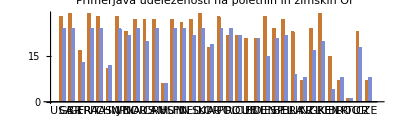

```mathematica
BarChart[primerjavaudelezenosti,ChartLabels->{Placed[okrajsave,Below],Placed[{""},Top]},PlotLabel->"Primerjava udeleženosti na poletnih in zimskih OI",AspectRatio->0.3,ImageSize->Full,BarSpacing->None,PlotTheme->"Default"]
```

```mathematica
najvisjaudelezenost = podatki[All,{1,12}]
```

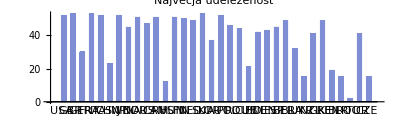

```mathematica
BarChart[najvisjaudelezenost,ChartLabels->{Placed[okrajsave,Below],Placed[{""},Top]},PlotLabel->"Največja udeleženost",AspectRatio->0.3,ImageSize->Full,PlotTheme->"Default"]
```

## Uspešnost na OI

```mathematica
skupno=podatki[All,{1,12,16}]
```

```mathematica
uspesnost=skupno//Query[All,<|#,"uspešnost"->#"vse medalje skupno"/#"udelezenost skupno"|>&]
```

```mathematica
PieChart[uspesnost[All,4],ChartLabels->Placed[okrajsave,"RadialCallout"],ChartStyle->27,ImageSize->Large]
```

-Graphics-

## Raziskava USA

```mathematica
USA=podatki[{1},All]
```

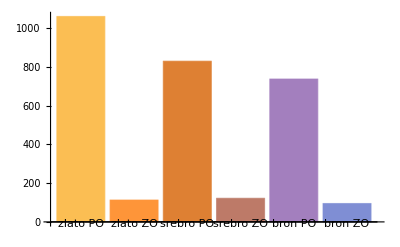

```mathematica
BarChart[USA[All,{3,8,4,9,5,10}],ChartLabels->Automatic,ChartStyle->Thickness[.5]]
```

```mathematica
medalje=podatki[1,{1,13,14,15}]
```

```mathematica
PieChart[medalje,ChartLabels->Automatic]
```

-Graphics-